```mathematica
Fsp[q_,R_]:=4/3*Pi*R^3*(Sin[q*R]-q*R*Cos[q*R])/(q*R)^3
```

```mathematica
F2gDAB[q_,xi_,H_]:= 1/(1+(q*xi)^2)^(3/2+H)
```

```mathematica
LogNorm[r_,mu_,sigma_]:=(√(2 π) sigma)^(-1)/r*Exp[-Log[r/mu]^2/(2*sigma^2)]
```

```mathematica
Integrate[LogNorm[r,mu,sigma],{r,0,Infinity},Assumptions->sigma>0 && mu>0]
```

1

```mathematica
Integrate[F2gDAB[q,xi,H]*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>0&&xi>0&&H>-1/2]
```

(2^(-1/2-H) r^(1/2+H) xi^(-5/2-H) BesselK[-1/2-H,r/xi])/Gamma[3/2+H]

```mathematica
Limit[Integrate[F2gDAB[q,xi,H]*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>0&&xi>0&&H>-1/2],H->-1/2+n,Assumptions->Integers[n]&&n>0]
```

(2^-n r^n xi^(-2-n) BesselK[-n,r/xi])/Gamma[1+n]

```mathematica
Limit[x^n*BesselK[-n,x],x->0,Assumptions->Integers[n]&&n>0]
```

Indeterminate

```mathematica
n
```

```mathematica
FullSimplify[Normal[Series[Integrate[F2gDAB[q,xi,H]*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>0&&xi>0&&H>-1/2],{r,0,0}]],Assumptions->q>=0&&r>0&&xi>0&&H>-1/2]
```

1/(xi^2+2 H xi^2)

```mathematica
CForm[Collect[FullSimplify[Normal[Series[Integrate[F2gDAB[q,xi,H]*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>0&&xi>0&&H>-1/2]-1/(xi^2+2 H xi^2),{r,0,6}]]/.r->u*xi,Assumptions->q>=0&&z>0&&xi>0&&H>-1/2],r]/.xi->A/.H->HH]
```

(u*((-8*u*(96*(-4 + HH)*HH - 12*HH*Power(u,2) + Power(u,4) + 30*(12 + Power(u,2))))/((-5 + 2*HH)*(-3 + 2*HH)*(-1 + 2*HH)*(1 + 2*HH)) + 
       (3*Power(u,2*HH)*(32*HH*(4 + HH) + 8*HH*Power(u,2) + Power(u,4) + 20*(6 + Power(u,2)))*Gamma(-0.5 - HH))/(Power(4,HH)*Gamma(3.5 + HH))))
    /(384.*Power(A,2))

```mathematica
Limit[(z ((2 z (12-8 H+z^2))/(3-2 H-12 H^2+8 H^3)+(4^-H z^(2 H) (6+4 H+z^2) Gamma[-1/2-H])/Gamma[5/2+H]))/(16 xi^2),H->-1/2+1]
```

(z^2 (-16-5 z^2+4 EulerGamma (8+z^2)-32 Log[2]-4 z^2 Log[2]+4 (8+z^2) Log[z]))/(128 xi^2)

```mathematica
FullSimplify[Gamma[-n]/Gamma[2+n],,Assumptions->Integer[n]]
```

```mathematica
Gamma[-n]/Gamma[2+n]
```

ComplexInfinity

```mathematica
CForm[FullSimplify[Normal[Series[Integrate[F2gDAB[q,xi,H]*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>0&&xi>0&&H>-1/2]-1/(xi^2+2 H xi^2),{r,0,3}]],Assumptions->q>=0&&r>0&&xi>0&&H>-1/2]]
```

(r*((8*r*xi)/(1 - 4*Power(H,2)) + (Power(r/xi,2*H)*(Power(r,2) + 2*(3 + 2*H)*Power(xi,2))*Gamma(-0.5 - H))/(Power(4,H)*Gamma(2.5 + H))))/
   (16.*Power(xi,5))

```mathematica
Integrate[Fsp[q,R]^2*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->q>=0&&r>=0&&R>0&&r<2*R]
```

```mathematica
Irsph[r_,R_,eta_]:=Module[{xi=r/(2*R)},Piecewise[{{eta^2 π R^4 (√(1-xi^2) (2+xi^2)-xi^2 (-4+xi^2) Log[xi/(1+√(1-xi^2))]),r<=2*R}},0]]
```

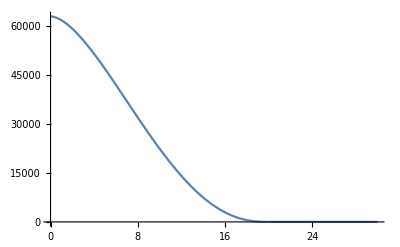

```mathematica
Plot[Irsph[r,10,1],{r,0,30},PlotRange->All]
```

```mathematica
GammaSD[x_,theta_,k_]:=1/theta*(x/theta)^(k-1)*Exp[-x/theta]/Gamma[k]
```

```mathematica
Integrate[Irsph[r,R,eta]*GammaSD[R,theta,k],{R,0,Infinity}]
```

$Aborted

```mathematica
Integrate[Irsph[r,R,eta]*LogNorm[R,mu,sigma],{R,0,Infinity}]
```

$Aborted

```mathematica
FullSimplify[Integrate[Fsp[q,R,eta,4/3*Pi*R^3]^2*q*lambda^2/(2*Pi),{q,0,qu}]]
```

(eta^2 lambda^2 π (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/qu^4

```mathematica
FullSimplify[Integrate[Fsp[q,R,eta,Vp]^2*q*lambda^2/(2*Pi),{q,0,qu}]]
```

(9 eta^2 lambda^2 Vp^2 (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/(16 π qu^4 R^6)

```mathematica
Limit[(eta^2 lambda^2 π (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/qu^4,qu->Infinity,Assumptions->R>0&&eta>0&&Vp>0]
```

2 eta^2 lambda^2 π R^4

```mathematica
Limit[(9 eta^2 lambda^2 Vp^2 (-1-2 qu^2 R^2+2 qu^4 R^4+Cos[2 qu R]+2 qu R Sin[2 qu R]))/(16 π qu^4 R^6),qu->Infinity,Assumptions->R>0&&eta>0&&Vp>0]
```

(9 eta^2 lambda^2 Vp^2)/(8 π R^2)

```mathematica
FullSimplify[Integrate[Fsp[q,R,eta,4/3*Pi*R^3]^2*q,{q,0,Infinity}]/(4*Pi),Assumptions->R>0]
```

eta^2 π R^4

```mathematica
ComplexExpand[Exp[I*a]]
```

Cos[a]+ⅈ Sin[a]

```mathematica
Integrate[BesselJ[0,q*r*zeta]*zeta*(1-Exp[I*nu*Sqrt[1-zeta^2]]),{zeta,0,1}]
```

∫_0^1 (1-ⅇ^(ⅈ nu √(1-zeta^2))) zeta BesselJ[0,q r zeta]ⅆzeta